```mathematica
Manipulate[Plot[{(1100-q)/100*a,(q+100)/200*(1-a), 1.8,(1100-q)/100*a-0.7,(q+100)/200*(1-a)+0.7},{q,0, 1100},PlotLegends->{"Demand", "Supply", "Price control", "Monopoly", "Monopsony"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{(100 (-1+23 a))/(1+a),-(12 (-1+a) a)/(1+a)},{0,0}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted}, Dashed,Dashed},GridLines->{{{500,Red}},None}, GridLinesStyle->Directive[Gray, Dotted, Thick]],{a,0.5,1}]
```

```mathematica
Manipulate[Plot[{(1100-q)/100*a,(q+100)/200*(1-a), 1.8,(1100-q*2)/100*a,(q*2+100)/200*(1-a)},{q,0, 1100},PlotLegends->{"Demand", "Supply", "Price control", "Monopsony", "Monopoly"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{(100 (-1+23 a))/(1+a),-(12 (-1+a) a)/(1+a)},{0,0}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted}, Dashed,Dashed},GridLines->{{{500,Red}},None}, GridLinesStyle->Directive[Gray, Dotted, Thick]],{a,0.5,1}]
```

Occupational licensing

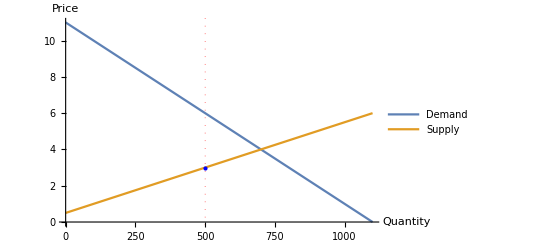

```mathematica
Plot[{(1100-q)/100,(q+100)/200},{q,0, 1100},PlotLegends->{"Demand", "Supply"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic},GridLines->{{{500,Red}},None}, GridLinesStyle->Directive[Gray, Dotted, Thick], Epilog->{Blue,PointSize@Large,Point[{{500,3}}]}]
```

```mathematica
Price control(minimum)
```

```mathematica
Manipulate[Plot[{(1100-q)/100*a,(q+100)/200*(1-a), 1.8},{q,0, 1300},PlotLegends->{"Demand", "Supply", "Price control"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{(100 (-1+23 a))/(1+a),-(12 (-1+a) a)/(1+a)},{-(100. (1.8-11. a))/a,1.8}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted}, Dashed,Dashed}, GridLinesStyle->Directive[Gray, Dotted, Thick]],{a,0.75,1}]
```

```mathematica
Solve[(1100-q)/100*a== 1.8,q]
```

{{q→-(100. (1.8-11. a))/a}}

```mathematica
Price control(maximum)
```

```mathematica
Manipulate[Plot[{(1100-q)/100*a,(q+100)/200*(1-a), 1.8},{q,0, 1300},PlotLegends->{"Demand", "Supply", "Price control"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{(100 (-1+23 a))/(1+a),-(12 (-1+a) a)/(1+a)},{(200. (1.8-0.5 (1.-1. a)))/(1.-1. a),1.8}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted}, Dashed,Dashed}, GridLinesStyle->Directive[Gray, Dotted, Thick]],{a,0.5,1}]
```

```mathematica
Monopsony and  control
```

```mathematica
Manipulate[Plot[{(1100-q)/100*a,(q+100)/200*(1-a), 1.8,(1100-q*2)/100*a},{q,0, 1100},PlotLegends->{"Demand", "Supply", "Price control", "Monopsony"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{(100 (-1+23 a))/(1+3 a),-(13 (-1+a) a)/(1+3 a)},{(200. (1.8-0.5 (1.-1. a)))/(1.-1. a),1.8}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted}, Dashed,Dashed}],{a,0.5,1}]
```

```mathematica
Solve[(1100-q*2)/100*a== (q+100)/200*(1-a),q]
```

{{q→(100 (-1+23 a))/(1+3 a)}}

```mathematica
Simplify[(((100 (-1+23 a))/(1+3 a))+100)/200*(1-a)]
```

-(13 (-1+a) a)/(1+3 a)

```mathematica
Monopoly and  control
```

```mathematica
Manipulate[Plot[{(1100-q)/100*a,(q+100)/200*(1-a), 1.8,(q*2+100)/200*(1-a)},{q,0, 1100},PlotLegends->{"Demand", "Supply", "Price control", "Monopoly"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{(100 (-1+23 a))/(1+a),-(12 (-1+a) a)/(1+a)},{0,0}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted},Dashed}],{a,0.5,1}]
```